```mathematica
P = UnitConvert[Quantity[10,"kPa"],"mmHg"]//N
```

75.0062 mmHg

3000.25 mmHg

```mathematica
P = UnitConvert[Quantity[4,"Bars"],"mmHg"]//N
a=6.809;
b = 935.86;
c = 238.73;
b/(a-Log10[QuantityMagnitude[P]]) - c
```

3000.25 mmHg

42.1536

```mathematica
P = UnitConvert[Quantity[4,"Bars"],"mmHg"]//N
a=7.4;
b = 362;
c = 178.7;
b/(a-Log10[QuantityMagnitude[P]]) - c
```

3000.25 mmHg

-86.42

```mathematica
P = UnitConvert[Quantity[4,"Bars"],"mmHg"]//N
a=11.6414;
b = 2510;
c = 253;
b/(a-Log10[QuantityMagnitude[P]]) - c
```

3000.25 mmHg

54.4382

```mathematica
P = UnitConvert[Quantity[4,"Bars"],"mmHg"]//N
a=6.80338;
b = 804;
c = 247.04;
b/(a-Log10[QuantityMagnitude[P]]) - c
```

3000.25 mmHg

-5.3244

```mathematica
Clear[x]
P = UnitConvert[Quantity[4,"Bars"],"mmHg"]//N
t = 10;
(*1 is the butane*)
a1 =6.80896;
b1=935.86;
c1=238.854;
(*2 is the propane*)
a2 = 6.80338;
b2= 804;
c2 = 247.04;
solx=Solve[QuantityMagnitude[P] == x*10^(a1-b1/(t+c1)) +(1- x)*10^(a2-b2/(t+c2)),x]
x =x/.solx[[1]]
```

3000.25 mmHg

{{x→0.479779}}

0.479779

```mathematica
P0b=UnitConvert[Quantity[10^(a1-b1/(t+c1)),"mmHg"],"bar"]
P0p=UnitConvert[Quantity[10^(a2-b2/(t+c2)),"mmHg"],"bar"]

Pb=UnitConvert[Quantity[x 10^(a1-b1/(t+c1)),"mmHg"],"bar"] 
Pp=UnitConvert[Quantity[(1-x) 10^(a2-b2/(t+c2)),"mmHg"],"bar"]
```

1.48999 bars

6.31488 bars

0.714867 bars

3.28513 bars

```mathematica
totalP = Pb+Pp
```

4. bars

```mathematica
(*Determine gaseous moles*)
Mb = Quantity[55.18, "g/mol"];
Mp = Quantity[44.1,"g/mol"];

V = Quantity[0.35,"Liters"];
R = Quantity[8.314 ,"J K^-1 mol^-1"];
T = UnitConvert[Quantity[10, "DegreesCelsius"]]//N;
nbg = UnitConvert[Pb V/(R T)]
npg = UnitConvert[Pp V/(R T)]
```

0.0106284 mol K/K

0.0488421 mol K/K

```mathematica
mbg = UnitConvert[nbg*Mb, "gram"]
mpg = UnitConvert[npg*Mp, "gram"]
```

0.586474 g K/K

2.15394 g K/K

```mathematica
(*Therefore this is the quantity of pressurant needed*)
mbg+mpg
```

2.74041 g K/K

```mathematica
rhobl = WolframAlphaQueryResults;
rhopl = WolframAlphaQueryResults;
Vbl =UnitConvert[ mbg/rhobl,"cm^3"]
Vpl =UnitConvert[ mpg/rhopl, "cm^3"]
```

0.973724 cm^3 K/K

3.70092 cm^3 K/K

```mathematica
Vbl + Vpl
```

4.67465 cm^3 K/K

p==10^(a21-b21/(c21+t1)) (1-x1)+10^(a11-b11/(c11+t1)) x1

```mathematica
p == x1*10^(a11-b11/(t1+c11)) +(1- x1)*10^(a21-b21/(t1+c21))
solx=Solve[p==10^(a21-b21/(c21+t1)) (1-x1)+10^(a11-b11/(c11+t1)) x1,{x1}]
```

p==10^(a21-b21/(c21+t1)) (1-x1)+10^(a11-b11/(c11+t1)) x1

{{x1→(10^(b11/(c11+t1)) (10^a21-10^(b21/(c21+t1)) p))/(10^(a21+b11/(c11+t1))-10^(a11+b21/(c21+t1)))}}

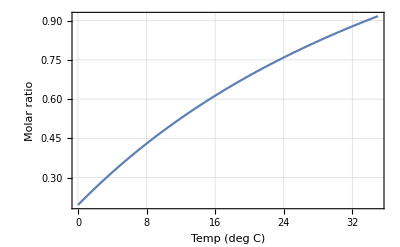

```mathematica
Plot[x1/.solx/.{a11-> a1, b11-> b1, c11-> c1, a21-> a2, b21-> b2, c21-> c2, p-> QuantityMagnitude[P]},{t1,0,35},Frame->True, GridLines->Automatic,FrameLabel->{"Temp (deg C)", "Molar ratio"}]
```